```mathematica
x1=-1.8072;
x2=3.8408;
x3=1;
a0=0;
a1=0.9316;
a2=-0.3635;
a3=1.1367;
A=Table[0,{x,4},{y,4}];
A[[1,1]]=-2*a0*x3;
A[[1,2]]=0;
A[[1,3]]=a0*x1+a1*x3;
A[[1,4]]=a0*x2-a2*x3;
A[[2,1]]=0;
A[[2,2]]=-2*a0*x3;
A[[2,3]]=a0*x2+a2*x3;
A[[2,4]]=-a0*x1+a1*x3;
A[[3,1]]=a0*x1+a1*x3;
A[[3,2]]=a0*x2+a2*x3;
A[[3,3]]=-a1*x1-a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
A[[3,4]]=a2*x1-a1*x2;
A[[4,1]]=a0*x2-a2*x3;
A[[4,2]]=-a0*x1+a1*x3;
A[[4,3]]=a2*x1-a1*x2;
A[[4,4]]=a1*x1+a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
A
```

{{0,0,0.9316,0.3635},{0,0,-0.3635,0.9316},{0.9316,-0.3635,3.64807,-2.92117},{0.3635,0.9316,-2.92117,-2.51137}}

```mathematica
q1=-2*a0*x3
q2=2*a0*x1
q3=2*a0*x2
q4=2*a1*x3
q5=2*a2*x3
q6=2*(a2*x1-a1*x2)
q7=-(a1*x1+a2*x2)
q8=1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2)
```

0

0.

0.

1.8632

-0.727

-5.84234

3.07972

0.56835

```mathematica
x1=-5.2262;
x2=3.8086;
x3=1;
a0=0;
a1=0.9283;
a2=0.3719;
a3=2.5989;
B=Table[0,{x,4},{y,4}];
B[[1,1]]=-2*a0*x3;
B[[1,2]]=0;
B[[1,3]]=a0*x1+a1*x3;
B[[1,4]]=a0*x2-a2*x3;
B[[2,1]]=0;
B[[2,2]]=-2*a0*x3;
B[[2,3]]=a0*x2+a2*x3;
B[[2,4]]=-a0*x1+a1*x3;
B[[3,1]]=a0*x1+a1*x3;
B[[3,2]]=a0*x2+a2*x3;
B[[3,3]]=-a1*x1-a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
B[[3,4]]=a2*x1-a1*x2;
B[[4,1]]=a0*x2-a2*x3;
B[[4,2]]=-a0*x1+a1*x3;
B[[4,3]]=a2*x1-a1*x2;
B[[4,4]]=a1*x1+a2*x2+1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2);
B
```

{{0,0,0.9283,-0.3719},{0,0,0.3719,0.9283},{0.9283,0.3719,4.73451,-5.47915},{-0.3719,0.9283,-5.47915,-2.13561}}

```mathematica
q1=-2*a0*x3
q2=2*a0*x1
q3=2*a0*x2
q4=2*a1*x3
q5=2*a2*x3
q6=2*(a2*x1-a1*x2)
q7=-(a1*x1+a2*x2)
q8=1/(2*x3)*(a3*x3^2-a0*x1^2-a0*x2^2)
```

0

0.

0.

1.8566

0.7438

-10.9583

3.43506

1.29945

```mathematica
myplot=ContourPlot3D[{A[[1, 1]]*x^2 + (A[[1, 2]] + A[[2, 1]])*x*y + (A[[1, 3]] + A[[3, 1]])*x*z + (A[[1, 4]] + A[[4, 1]])*x + A[[2, 2]]*y^2 + (A[[2, 3]] + A[[3, 2]])*y*z + (A[[2, 4]] + A[[4, 2]])*y + A[[3, 3]]*z^2 + (A[[3, 4]] + A[[4, 3]])*z + A[[4, 4]] == 0, B[[1, 1]]*x^2 + (B[[1, 2]] + B[[2, 1]])*x*y + (B[[1, 3]] + B[[3, 1]])*x*z + (B[[1, 4]] + B[[4, 1]])*x + B[[2, 2]]*y^2 + (B[[2, 3]] + B[[3, 2]])*y*z + (B[[2, 4]] + B[[4, 2]])*y + B[[3, 3]]*z^2 + (B[[3, 4]] + B[[4, 3]])*z + B[[4, 4]] == 0}, {x, -10, 10}, {y, -10, 10}, {z, -10, 10}, PerformanceGoal -> "Quality", MeshStyle -> Gray, Mesh -> 0, Boxed -> False, Axes -> True, AxesLabel -> {X, Y, Z}, MaxRecursion -> 15, PlotPoints -> 50, PlotRange -> Automatic, ContourStyle -> {{Magenta, Opacity[0.5]}, {Orange,Opacity[0.5]}}];
Show[myplot]
```

-Graphics3D-

```mathematica
eigenvalues=Eigenvalues[A];
eigenvectors=Eigenvectors[A];
transformatrix=Transpose[{eigenvectors[[3]],eigenvectors[[1]],eigenvectors[[4]], eigenvectors[[2]]}];
```

```mathematica
afterA=Transpose[transformatrix].A.transformatrix;
MatrixForm[afterA]
```

(0.254404 | 1.47798×10^-15 | 1.76161×10^-15 | -1.9984×10^-15
1.4988×10^-15 | 5.0126 | -3.33067×10^-16 | 4.44089×10^-16
1.76291×10^-15 | -5.1608×10^-16 | -0.199499 | 7.54605×10^-16
-2.10942×10^-15 | 8.88178×10^-16 | 6.66134×10^-16 | -3.9308)

```mathematica
afterB=Transpose[transformatrix].B.transformatrix;
MatrixForm[afterB]
```

(0.0469538 | 0.227386 | 0.217299 | 0.54505
0.227386 | 7.55289 | 0.777174 | 1.82646
0.217299 | 0.777174 | 0.00948795 | -0.311468
0.54505 | 1.82646 | -0.311468 | -5.01043)

```mathematica
Clear[V];Clear[u];Clear[v];
V={(u+afterA[[1,1]]*v)/afterA[[1,1]], (u*v-afterA[[2,2]])/afterA[[2,2]], (u-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
```

```mathematica
goalformula=Collect[Expand[V.afterB.V], {u^2, u}]
```

-2.96154+3.32585 v-0.431719 v^2+u (-6.97081-5.28886 v+0.144614 v^2)+u^2 (8.49528+2.07544 v+0.210482 v^2)

```mathematica
delta=Expand[(-6.970809729285728-5.2888645379497925 v+0.14461407235964185 v^2)^2-4*(8.495277494480582+2.0754355002622624 v+0.21048235873913695 v^2)*(-2.9615355215451142+3.3258481753650733 v-0.4317186537616595 v^2)];
```

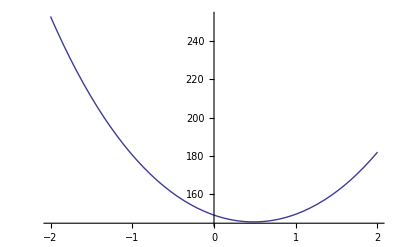

```mathematica
Plot[delta, {v,-2, 2}]
```

```mathematica
Solve[delta==0, v]
```

{{v→0.485055-4.41226 ⅈ},{v→0.485055+4.41226 ⅈ},{v→0.485055-4.41226 ⅈ},{v→0.485055+4.41226 ⅈ}}

```mathematica
u1=(-(-6.970809729285728-5.2888645379497925 v+0.14461407235964185 v^2)+Sqrt[delta])/(2*(8.495277494480582+2.0754355002622624 v+0.21048235873913695 v^2));
u2=(-(-6.970809729285728-5.2888645379497925 v+0.14461407235964185 v^2)-Sqrt[delta])/(2*(8.495277494480582+2.0754355002622624 v+0.21048235873913695 v^2));
```

```mathematica
afterP1={(u1+afterA[[1,1]]*v)/afterA[[1,1]], (u1*v-afterA[[2,2]])/afterA[[2,2]], (u1-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u1*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
afterP2={(u2+afterA[[1,1]]*v)/afterA[[1,1]], (u2*v-afterA[[2,2]])/afterA[[2,2]], (u2-afterA[[1,1]]*v)/Sqrt[-afterA[[1,1]]*afterA[[3,3]]], (u2*v+afterA[[2,2]])/Sqrt[-afterA[[2,2]]*afterA[[4,4]]]};
```

```mathematica
P1=transformatrix.afterP1;
P2=transformatrix.afterP2;
```

```mathematica
Branch1=Graphics3D[{PointSize[0.011],Black,Point[Table[{P2[[1]]/P2[[4]],P2[[2]]/P2[[4]],P2[[3]]/P2[[4]]},{v,4.5,250, 0.01}]]},Axes -> True, Boxed -> False,AxesLabel -> {X, Y, Z}];
Branch2=Graphics3D[{PointSize[0.011],Black,Point[Table[{P2[[1]]/P2[[4]],P2[[2]]/P2[[4]],P2[[3]]/P2[[4]]},{v, -200,1.4, 0.01}]]},Axes -> True, Boxed -> False,AxesLabel -> {X, Y, Z}];
Show[Branch1,Branch2,myplot]
```

-Graphics3D-